```mathematica
n=100;
```

```mathematica
points=Table[{(2(1+0.4RandomReal[]) Cos[t(1+0.1RandomReal[])]),(1(1+0.4RandomReal[]) Sin[t(1+0.1RandomReal[])])},{t,0,2 Pi-(2 Pi)/n,(2 Pi)/n}]//N;
```

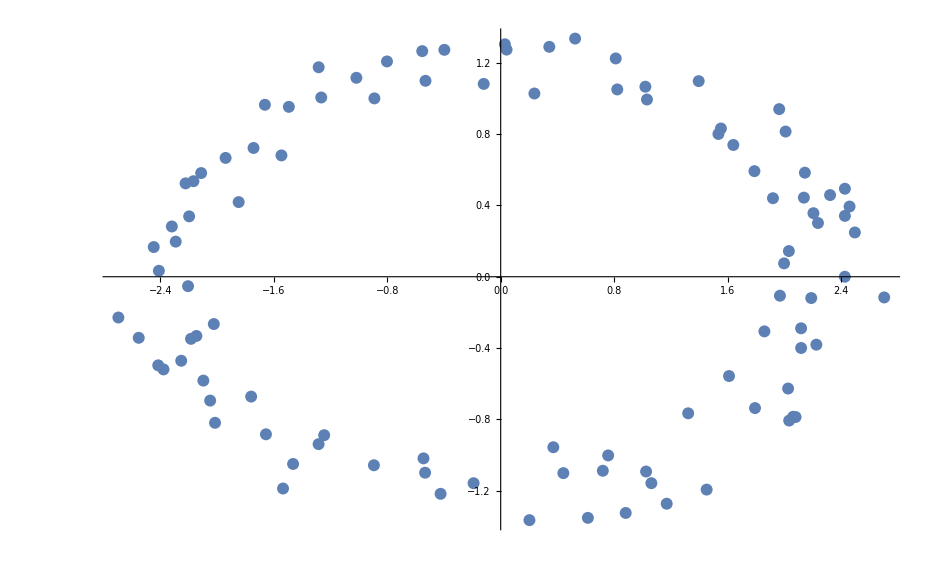

```mathematica
p1=ListPlot[points]
```

```mathematica
x2=Table[points[[i,1]]*points[[i,1]],{i,n}];
```

```mathematica
y2=Table[points[[i,2]]*points[[i,2]],{i,n}];
```

```mathematica
xy=Table[points[[i,1]]*points[[i,2]],{i,n}];
```

```mathematica
x=Table[points[[i,1]],{i,n}];
```

```mathematica
y=Table[points[[i,2]],{i,n}];
```

```mathematica
ones=Table[1,{i,n}];
```

```mathematica
zeros=Table[0,{i,n}];
```

```mathematica
a=Transpose[{x2,y2, xy,x,y}];
```

```mathematica
MatrixForm[a]
```

(5.88798 | 0. | 0. | 2.42652 | 0.
3.9923 | 0.00562704 | 0.149883 | 1.99808 | 0.0750136
4.12853 | 0.0207128 | 0.292427 | 2.03188 | 0.14392
6.23556 | 0.0616364 | 0.61995 | 2.49711 | 0.248267
5.0042 | 0.0908557 | 0.674285 | 2.23701 | 0.301423
4.56929 | 0.196841 | 0.94838 | 2.13759 | 0.443668
3.68469 | 0.193938 | 0.845342 | 1.91955 | 0.440384
5.39324 | 0.209769 | 1.06364 | 2.32234 | 0.458005
3.20058 | 0.350596 | 1.0593 | 1.78902 | 0.592112
4.59979 | 0.340493 | 1.25148 | 2.14471 | 0.583518
4.03458 | 0.663102 | 1.63565 | 2.00863 | 0.814311
2.3567 | 0.641256 | 1.22933 | 1.53515 | 0.800785
3.85594 | 0.883797 | 1.84604 | 1.96366 | 0.940105
2.69029 | 0.546033 | 1.21202 | 1.64021 | 0.738941
2.4107 | 0.691062 | 1.29071 | 1.55264 | 0.831301
1.94882 | 1.20336 | 1.53138 | 1.396 | 1.09698
1.04085 | 1.13567 | 1.08723 | 1.02022 | 1.06568
1.06361 | 0.987983 | 1.0251 | 1.03131 | 0.993973
0.67572 | 1.10351 | 0.863519 | 0.822022 | 1.05048
0.65801 | 1.49875 | 0.99307 | 0.811178 | 1.22423
0.275326 | 1.78387 | 0.700818 | 0.524715 | 1.33562
0.117558 | 1.66248 | 0.442084 | 0.342867 | 1.28937
0.0564806 | 1.05596 | 0.244216 | 0.237656 | 1.0276
0.000867822 | 1.69986 | 0.0384081 | 0.0294588 | 1.30379
0.00173035 | 1.62266 | 0.0529884 | 0.0415975 | 1.27384
0.0143187 | 1.16951 | -0.129406 | -0.119661 | 1.08144
0.281147 | 1.20726 | -0.582596 | -0.530233 | 1.09876
0.157736 | 1.61945 | -0.505417 | -0.39716 | 1.27258
0.306005 | 1.6008 | -0.699895 | -0.553177 | 1.26523
0.642635 | 1.45788 | -0.967927 | -0.801645 | 1.20743
0.79288 | 1.00052 | -0.89067 | -0.890438 | 1.00026
1.03489 | 1.24493 | -1.13506 | -1.01729 | 1.11577
1.60093 | 1.01065 | -1.272 | -1.26528 | 1.00531
1.64702 | 1.38022 | -1.50773 | -1.28336 | 1.17483
2.23102 | 0.907779 | -1.42312 | -1.49366 | 0.952774
3.0366 | 0.521497 | -1.2584 | -1.74258 | 0.722147
2.38948 | 0.463 | -1.05182 | -1.54579 | 0.680441
2.76367 | 0.930127 | -1.6033 | -1.66243 | 0.964431
3.76154 | 0.444091 | -1.29247 | -1.93947 | 0.666401
4.45962 | 0.338183 | -1.22808 | -2.11178 | 0.581535
3.41287 | 0.175224 | -0.773316 | -1.84739 | 0.418598
4.69293 | 0.287063 | -1.16068 | -2.16632 | 0.535783
4.93631 | 0.274131 | -1.16327 | -2.22178 | 0.523575
5.37609 | 0.0794685 | -0.653628 | -2.31864 | 0.281902
4.82459 | 0.114703 | -0.743905 | -2.19649 | 0.338678
5.9839 | 0.0277383 | -0.407411 | -2.4462 | 0.166548
5.24968 | 0.0387553 | -0.451058 | -2.29122 | 0.196864
4.85865 | 0.00279674 | 0.116569 | -2.20423 | -0.0528842
7.26544 | 0.0522884 | 0.616359 | -2.69545 | -0.228667
5.80825 | 0.0011197 | -0.0806442 | -2.41003 | 0.0334619
4.60275 | 0.110247 | 0.712348 | -2.1454 | -0.332035
4.76794 | 0.121296 | 0.760483 | -2.18356 | -0.348276
4.09074 | 0.0703886 | 0.536602 | -2.02256 | -0.265309
5.65151 | 0.269968 | 1.2352 | -2.37729 | -0.519584
6.51296 | 0.117318 | 0.87412 | -2.55205 | -0.342517
5.83003 | 0.246838 | 1.19961 | -2.41455 | -0.496828
5.07284 | 0.221978 | 1.06116 | -2.2523 | -0.471146
3.09521 | 0.45168 | 1.18239 | -1.75932 | -0.672071
4.39473 | 0.339274 | 1.22107 | -2.09636 | -0.582472
4.19581 | 0.482333 | 1.4226 | -2.04837 | -0.694502
4.05622 | 0.670854 | 1.64959 | -2.01401 | -0.819056
2.14278 | 1.10235 | 1.53691 | -1.46382 | -1.04993
2.73928 | 0.780717 | 1.4624 | -1.65508 | -0.883582
2.35525 | 1.41028 | 1.82251 | -1.53468 | -1.18755
1.64822 | 0.881252 | 1.20519 | -1.28383 | -0.93875
1.54882 | 0.789396 | 1.10573 | -1.24452 | -0.888479
0.283962 | 1.2077 | 0.585612 | -0.532881 | -1.09895
0.179581 | 1.48195 | 0.515878 | -0.42377 | -1.21735
0.799066 | 1.11756 | 0.944989 | -0.893905 | -1.05715
0.296169 | 1.03745 | 0.554311 | -0.544214 | -1.01855
0.0365268 | 1.34049 | 0.221277 | -0.19112 | -1.15779
0.0410916 | 1.86338 | -0.276712 | 0.202711 | -1.36506
0.195196 | 1.21292 | -0.486576 | 0.44181 | -1.10132
0.377868 | 1.82846 | -0.831214 | 0.61471 | -1.3522
0.776883 | 1.75465 | -1.16754 | 0.88141 | -1.32463
1.05087 | 1.1931 | -1.11973 | 1.02512 | -1.09229
1.36999 | 1.62029 | -1.4899 | 1.17047 | -1.27291
0.137807 | 0.914242 | -0.35495 | 0.371224 | -0.95616
0.518397 | 1.18378 | -0.78337 | 0.719998 | -1.08802
0.574188 | 1.00415 | -0.759324 | 0.757752 | -1.00207
2.10864 | 1.4249 | -1.73338 | 1.45211 | -1.19369
1.12868 | 1.34012 | -1.22987 | 1.06239 | -1.15764
1.74734 | 0.586445 | -1.01228 | 1.32187 | -0.765797
2.59204 | 0.31007 | -0.8965 | 1.60998 | -0.556839
4.25079 | 0.616786 | -1.61921 | 2.06175 | -0.785357
3.21524 | 0.54245 | -1.32065 | 1.79311 | -0.736512
4.13744 | 0.650564 | -1.64063 | 2.03407 | -0.806575
4.10618 | 0.393031 | -1.27038 | 2.02637 | -0.626922
4.9532 | 0.14507 | -0.847679 | 2.22558 | -0.38088
4.32204 | 0.618939 | -1.63557 | 2.07895 | -0.786727
4.48748 | 0.159656 | -0.846435 | 2.11837 | -0.399569
3.87643 | 0.0113064 | -0.209353 | 1.96887 | -0.106332
3.45704 | 0.0938605 | -0.569631 | 1.85931 | -0.306367
4.4858 | 0.0836168 | -0.612444 | 2.11797 | -0.289166
4.79421 | 0.0142647 | -0.261511 | 2.18957 | -0.119435
7.31149 | 0.0134674 | -0.313794 | 2.70398 | -0.116049
5.88961 | 0.116453 | 0.828168 | 2.42685 | 0.341252
4.86242 | 0.127009 | 0.785858 | 2.20509 | 0.356384
6.04993 | 0.155007 | 0.968391 | 2.45966 | 0.393709
5.88949 | 0.24359 | 1.19776 | 2.42683 | 0.493548)

```mathematica
Transpose[a].a//MatrixForm
```

(1316.21 | 104.783 | 40.2213 | 26.2255 | 0.563607
104.783 | 79.8122 | -5.04992 | 4.75003 | 1.82855
40.2213 | -5.04992 | 104.783 | 0.563607 | 4.75003
26.2255 | 4.75003 | 0.563607 | 298.42 | 3.14992
0.563607 | 1.82855 | 4.75003 | 3.14992 | 69.4719)

```mathematica
coefs=LinearSolve[Transpose[a].a,Transpose[a].ones]
```

{0.176033,0.638387,-0.0072136,0.00444945,0.00985546}

```mathematica
p2=ContourPlot[coefs[[1]]*x^2+coefs[[2]]*y^2+coefs[[3]]*x*y+coefs[[4]]*x+coefs[[5]]*y-1==0,{x,-4,4},{y,-4,4},ColorFunction->Hue,PlotStyle->{Red,Thick}];
```

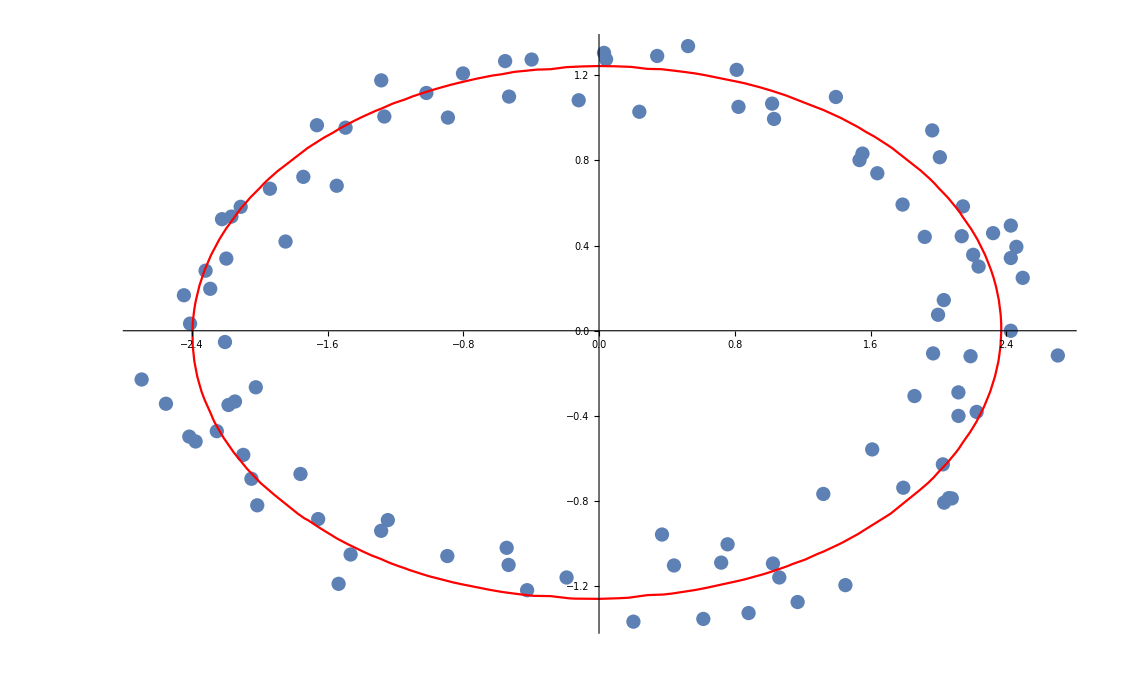

```mathematica
Show[p1,p2]
```